```mathematica
(* from soundView_export2.nb *)
(* created at 2012/3/11 *)
(* used for d-thesis *)
```

```mathematica
(* 離散ユニットステップフィルタ *)
step[n_Integer?Positive]:=1+Sign[Sin[π Range[1,-1,-2/n]//Most]]
(* 実関数の複素化 *)
wind[li_List]:=InverseFourier[Fourier[li]*step[Length[li]]]
```

```mathematica
wavname="guitar";
wavfile=Import[ wavname<>".wav"];
li=wavfile⟦1⟧⟦1⟧⟦1⟧;
len=li//Length
compli=wind[li];
```

144567

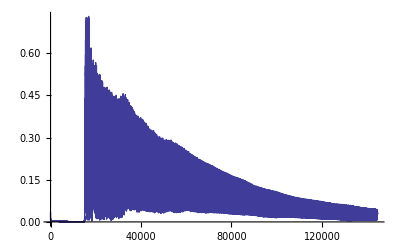

```mathematica
ListLinePlot[Abs[compli],PlotRange->{All,All}]
```

{20000,21000}

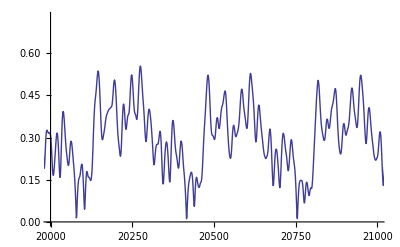

```mathematica
mainrange={20000,21000}
ListLinePlot[Abs[compli],PlotRange->{mainrange,All}]
```

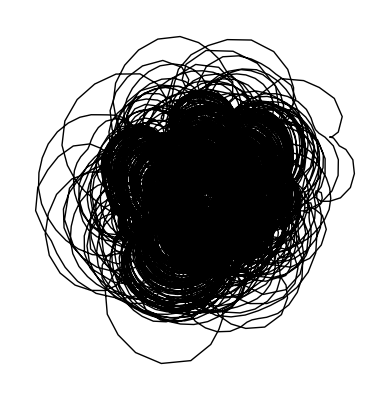

```mathematica
ListLinePlot[{Re[compli],Im[compli]}ᵀ,PlotRange->All,AspectRatio->Automatic,Axes->False,PlotStyle->Black]
```

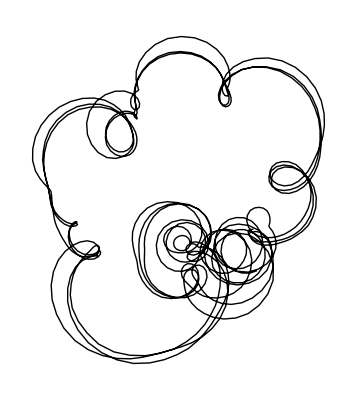

```mathematica
ListLinePlot[Take[{Re[compli],Im[compli]}ᵀ,mainrange],PlotRange->All,AspectRatio->Automatic,Axes->None,PlotStyle->Black]
```